```mathematica
Subscript[ψ, n]=√(2/a)Sin[nπ/a x];
```

```mathematica
Sin[3.4]
```

-0.255541

```mathematica
Plus[2,2]
```

```mathematica
4
```

```mathematica
LaplaceTransform[1/t^2,t,s]
```

LaplaceTransform[1/t^2,t,s]

```mathematica
Mean[{1,2,2,7,2,4}]
```

3

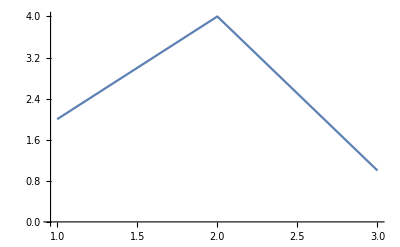

```mathematica
ListLinePlot[{{1,2},{2,4},{3,1}}]
```

```mathematica
Inverse[{{1,2,3},{4,5,2},{2,1,1}}]
```

(-1/5 | -1/15 | 11/15
0 | 1/3 | -2/3
2/5 | -1/5 | 1/5)

```mathematica
f=x^n
```

x^n

```mathematica
D[f,x]
```

n x^(-1+n)

```mathematica
Subscript[x, c]=(Subscript[x, e]-α^2 Subscript[x, p])/(1-α^2);Subscript[y, c]=(Subscript[y, e]-α^2 Subscript[y, p])/(1-α^2);Subscript[z, c]=(Subscript[z, e]-α^2 Subscript[z, p])/(1-α^2);
```

```mathematica
Subscript[r, c]=Norm[{Subscript[x, c],Subscript[y, c],Subscript[z, c]}];FullSimplify[Subscript[r, c],0<=α<=1]
```

√((Abs[x_e-α^2 x_p]^2+Abs[y_e-α^2 y_p]^2+Abs[z_e-α^2 z_p]^2)/((-1+α^2)^2))

```mathematica
Subscript[r, pe]=Norm[{Subscript[x, p]-Subscript[x, e],Subscript[y, p]-Subscript[y, e],Subscript[z, p]-Subscript[z, e]}]
```

√(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2)

```mathematica
β=α/(1-α^2)Subscript[r, pe]/Subscript[r, c];FullSimplify[β]
```

-(α Abs[-1+α^2] √((Abs[x_e-x_p]^2+Abs[y_e-y_p]^2+Abs[z_e-z_p]^2)/(Abs[x_e-α^2 x_p]^2+Abs[y_e-α^2 y_p]^2+Abs[z_e-α^2 z_p]^2)))/(-1+α^2)

```mathematica
V=Subscript[r, c]^2(1-β)^2;FullSimplify[V]
```

1/((-1+α^2)^2 Abs[-1+α^2]^2)(α Abs[-1+α^2] √(Abs[x_e-x_p]^2+Abs[y_e-y_p]^2+Abs[z_e-z_p]^2)+(-1+α^2) √(Abs[x_e-α^2 x_p]^2+Abs[y_e-α^2 y_p]^2+Abs[z_e-α^2 z_p]^2))^2

```mathematica
Subscript[V, xe]=D[V,Subscript[x, e]];FullSimplify[Subscript[V, xe]]
```

-((2 (α Abs[-1+α^2] √(Abs[x_e-x_p]^2+Abs[y_e-y_p]^2+Abs[z_e-z_p]^2)+(-1+α^2) √(Abs[x_e-α^2 x_p]^2+Abs[y_e-α^2 y_p]^2+Abs[z_e-α^2 z_p]^2)) (α Abs[x_e-x_p] (Abs[x_e-α^2 x_p]^2+Abs[y_e-α^2 y_p]^2+Abs[z_e-α^2 z_p]^2) Abs'[-x_e+x_p]+Abs[x_e-α^2 x_p] √((Abs[x_e-x_p]^2+Abs[y_e-y_p]^2+Abs[z_e-z_p]^2) (Abs[x_e-α^2 x_p]^2+Abs[y_e-α^2 y_p]^2+Abs[z_e-α^2 z_p]^2)) Abs'[(-x_e+α^2 x_p)/(-1+α^2)]))/((-1+α^2)^2 Abs[-1+α^2] √(Abs[x_e-x_p]^2+Abs[y_e-y_p]^2+Abs[z_e-z_p]^2) (Abs[x_e-α^2 x_p]^2+Abs[y_e-α^2 y_p]^2+Abs[z_e-α^2 z_p]^2)))

```mathematica
Subscript[V, ye]=D[V,Subscript[y, e]]
```

(2 Abs[(y_e-α^2 y_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(y_e-α^2 y_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) ((α Abs[-y_e+y_p] Abs'[-y_e+y_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))+(α Abs[(y_e-α^2 y_p)/(1-α^2)] √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs'[(y_e-α^2 y_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2)))

```mathematica
Subscript[V, ze]=D[V,Subscript[z, e]]
```

(2 Abs[(z_e-α^2 z_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(z_e-α^2 z_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) ((α Abs[-z_e+z_p] Abs'[-z_e+z_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))+(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs[(z_e-α^2 z_p)/(1-α^2)] Abs'[(z_e-α^2 z_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2)))

```mathematica
Subscript[V, xp]=D[V,Subscript[x, p]]
```

-(2 α^2 Abs[(x_e-α^2 x_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(x_e-α^2 x_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) (-(α Abs[-x_e+x_p] Abs'[-x_e+x_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))-(α^3 Abs[(x_e-α^2 x_p)/(1-α^2)] √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs'[(x_e-α^2 x_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2)))

```mathematica
Subscript[V, yp]=D[V,Subscript[y, p]]
```

-(2 α^2 Abs[(y_e-α^2 y_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(y_e-α^2 y_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) (-(α Abs[-y_e+y_p] Abs'[-y_e+y_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))-(α^3 Abs[(y_e-α^2 y_p)/(1-α^2)] √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs'[(y_e-α^2 y_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2)))

```mathematica
Subscript[V, zp]=D[V,Subscript[z, p]]
```

-(2 α^2 Abs[(z_e-α^2 z_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(z_e-α^2 z_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) (-(α Abs[-z_e+z_p] Abs'[-z_e+z_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))-(α^3 √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs[(z_e-α^2 z_p)/(1-α^2)] Abs'[(z_e-α^2 z_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2)))

```mathematica
Subscript[ρ, e]=√(Subscript[V, xe]^2+Subscript[V, ye]^2+Subscript[V, ze]^2)
```

√(((2 Abs[(x_e-α^2 x_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(x_e-α^2 x_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) ((α Abs[-x_e+x_p] Abs'[-x_e+x_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))+(α Abs[(x_e-α^2 x_p)/(1-α^2)] √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs'[(x_e-α^2 x_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2))))^2+((2 Abs[(y_e-α^2 y_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(y_e-α^2 y_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) ((α Abs[-y_e+y_p] Abs'[-y_e+y_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))+(α Abs[(y_e-α^2 y_p)/(1-α^2)] √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs'[(y_e-α^2 y_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2))))^2+((2 Abs[(z_e-α^2 z_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(z_e-α^2 z_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) ((α Abs[-z_e+z_p] Abs'[-z_e+z_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))+(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs[(z_e-α^2 z_p)/(1-α^2)] Abs'[(z_e-α^2 z_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2))))^2)

```mathematica
Subscript[ρ, p]=√(Subscript[V, xp]^2+Subscript[V, yp]^2+Subscript[V, zp]^2)
```

√((-(2 α^2 Abs[(x_e-α^2 x_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(x_e-α^2 x_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) (-(α Abs[-x_e+x_p] Abs'[-x_e+x_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))-(α^3 Abs[(x_e-α^2 x_p)/(1-α^2)] √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs'[(x_e-α^2 x_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2))))^2+(-(2 α^2 Abs[(y_e-α^2 y_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(y_e-α^2 y_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) (-(α Abs[-y_e+y_p] Abs'[-y_e+y_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))-(α^3 Abs[(y_e-α^2 y_p)/(1-α^2)] √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs'[(y_e-α^2 y_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2))))^2+(-(2 α^2 Abs[(z_e-α^2 z_p)/(1-α^2)] (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)))^2 Abs'[(z_e-α^2 z_p)/(1-α^2)])/(1-α^2)+2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2) (1-(α √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2))/((1-α^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))) (-(α Abs[-z_e+z_p] Abs'[-z_e+z_p])/((1-α^2) √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) √(Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2))-(α^3 √(Abs[-x_e+x_p]^2+Abs[-y_e+y_p]^2+Abs[-z_e+z_p]^2) Abs[(z_e-α^2 z_p)/(1-α^2)] Abs'[(z_e-α^2 z_p)/(1-α^2)])/((1-α^2)^2 (Abs[(x_e-α^2 x_p)/(1-α^2)]^2+Abs[(y_e-α^2 y_p)/(1-α^2)]^2+Abs[(z_e-α^2 z_p)/(1-α^2)]^2)^(3/2))))^2)

```mathematica
FullSimplify[-α Subscript[ρ, e]+Subscript[ρ, p]]
```

$Aborted

```mathematica
β=√((Subscript[x, c2]-Subscript[x, c1])^2+(Subscript[y, c2]-Subscript[y, c1])^2+(Subscript[z, c2]-Subscript[z, c1])^2);γ=√((Subscript[x, c2]-Subscript[x, c1])^2+(Subscript[z, c2]-Subscript[z, c1])^2);
```

```mathematica
R={{(-(Subscript[y, c2]-Subscript[y, c1])(Subscript[x, c2]-Subscript[x, x1]))/(β γ),((Subscript[x, c2]-Subscript[x, c1])^2+(Subscript[z, c2]-Subscript[z, c1])^2)/(β γ),(-(Subscript[y, c2]-Subscript[y, c1])(Subscript[z, c2]-Subscript[z, x1]))/(β γ)},{(Subscript[z, c2]-Subscript[z, c1])/γ,0,(Subscript[x, c1]-Subscript[x, c2])/γ},{(Subscript[x, c2]-Subscript[x, c1])/β,(Subscript[y, c2]-Subscript[y, c1])/β,(Subscript[z, c2]-Subscript[z, c1])/β}}
```

{{((x_c2-x_x1) (y_c1-y_c2))/(√((-x_c1+x_c2)^2+(-z_c1+z_c2)^2) √((-x_c1+x_c2)^2+(-y_c1+y_c2)^2+(-z_c1+z_c2)^2)),(√((-x_c1+x_c2)^2+(-z_c1+z_c2)^2))/(√((-x_c1+x_c2)^2+(-y_c1+y_c2)^2+(-z_c1+z_c2)^2)),((y_c1-y_c2) (z_c2-z_x1))/(√((-x_c1+x_c2)^2+(-z_c1+z_c2)^2) √((-x_c1+x_c2)^2+(-y_c1+y_c2)^2+(-z_c1+z_c2)^2))},{(-z_c1+z_c2)/(√((-x_c1+x_c2)^2+(-z_c1+z_c2)^2)),0,(x_c1-x_c2)/(√((-x_c1+x_c2)^2+(-z_c1+z_c2)^2))},{(-x_c1+x_c2)/(√((-x_c1+x_c2)^2+(-y_c1+y_c2)^2+(-z_c1+z_c2)^2)),(-y_c1+y_c2)/(√((-x_c1+x_c2)^2+(-y_c1+y_c2)^2+(-z_c1+z_c2)^2)),(-z_c1+z_c2)/(√((-x_c1+x_c2)^2+(-y_c1+y_c2)^2+(-z_c1+z_c2)^2))}}

```mathematica
FullSimplify[MatrixForm[R]]
```

(((x_c2-x_x1) (y_c1-y_c2))/(√((x_c1-x_c2)^2+(z_c1-z_c2)^2) √((x_c1-x_c2)^2+(y_c1-y_c2)^2+(z_c1-z_c2)^2)) | (√((x_c1-x_c2)^2+(z_c1-z_c2)^2))/(√((x_c1-x_c2)^2+(y_c1-y_c2)^2+(z_c1-z_c2)^2)) | ((y_c1-y_c2) (z_c2-z_x1))/(√((x_c1-x_c2)^2+(z_c1-z_c2)^2) √((x_c1-x_c2)^2+(y_c1-y_c2)^2+(z_c1-z_c2)^2))
(-z_c1+z_c2)/(√((x_c1-x_c2)^2+(z_c1-z_c2)^2)) | 0 | (x_c1-x_c2)/(√((x_c1-x_c2)^2+(z_c1-z_c2)^2))
(-x_c1+x_c2)/(√((x_c1-x_c2)^2+(y_c1-y_c2)^2+(z_c1-z_c2)^2)) | (-y_c1+y_c2)/(√((x_c1-x_c2)^2+(y_c1-y_c2)^2+(z_c1-z_c2)^2)) | (-z_c1+z_c2)/(√((x_c1-x_c2)^2+(y_c1-y_c2)^2+(z_c1-z_c2)^2)))

```mathematica
Subscript[x, 0]=(Subscript[y, c2]-Subscript[y, c1])(Subscript[x, c1](Subscript[x, c2]-Subscript[x, c1])+Subscript[z, c1](Subscript[z, c2]-Subscript[z, c1]))-Subscript[y, c1]((Subscript[x, c2]-Subscript[x, c1])^2+(Subscript[z, c2]-Subscript[z, c1])^2);Subscript[y, 0]=Subscript[x, c2] Subscript[z, c1]-Subscript[x, c1] Subscript[z, c2];
```

```mathematica
μ=-1+√((Subscript[x, 0]^2+Subscript[y, 0]^2)/(Subscript[r, c1]^2-k^2 β^2));
```

```mathematica
V=Subscript[x, c1]^2+Subscript[y, c1]^2+Subscript[z, c1]^2+Subscript[r, c1]^2+{Subscript[x, c1],Subscript[y, c1],Subscript[z, c1]}Transpose[R]Transpose[{{Subscript[x, 0]/(1+μ),Subscript[y, 0]/(1+μ),k β}}];
```

```mathematica
Subscript[C, 1]=(x-Subscript[x, c1])^2+(y-Subscript[y, c1])^2-Subscript[r, c1]^2;Subscript[C, 2]=(x-Subscript[x, c2])^2+(y-Subscript[y, c2])^2-Subscript[r, c2]^2;
L=Subscript[C, 1]-Subscript[C, 2];FullSimplify[L]
```

-r_c1^2+r_c2^2+(x-x_c1)^2-(x-x_c2)^2+(y-y_c1)^2-(y-y_c2)^2

```mathematica
Solve[L==0,y]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-r_c1^2+r_c2^2+(x-x_c1)^2-(x-x_c2)^2+(y-y_c1)^2-(y-y_c2)^2==0,y]

```mathematica
Solve[Subscript[C, 1]==0 && Subscript[C, 2]==0]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-r_c1^2+(x-x_c1)^2+(y-y_c1)^2==0&&-r_c2^2+(x-x_c2)^2+(y-y_c2)^2==0]

```mathematica
Solve[L==0 && {x,y}∈Circle[{Subscript[x, c1],Subscript[y, c1]},Subscript[r, c1]],y]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-r_c1^2+r_c2^2+(x-x_c1)^2-(x-x_c2)^2+(y-y_c1)^2-(y-y_c2)^2==0&&{x,y}∈Circle[{x_c1,y_c1},r_c1],y]

```mathematica
yint=((x-Subscript[x, c1])^2-(x-Subscript[x, c2])^2-Subscript[r, c1]^2+Subscript[r, c2]^2+Subscript[y, c1]^2-Subscript[y, c2]^2)/(2*Subscript[y, c1]-2*Subscript[y, c2])
```

(-r_c1^2+r_c2^2+(x-x_c1)^2-(x-x_c2)^2+y_c1^2-y_c2^2)/(2 y_c1-2 y_c2)

```mathematica
Subscript[C, 1]/.y->yint
```

```mathematica
-Subscript[r, c1]^2+(x-Subscript[x, c1])^2+((-Subscript[r, c1]^2+Subscript[r, c2]^2+(x-Subscript[x, c1])^2-(x-Subscript[x, c2])^2+Subscript[y, c1]^2-Subscript[y, c2]^2)/(2 Subscript[y, c1]-2 Subscript[y, c2])-Subscript[(-Subscript[r, c1]^2+Subscript[r, c2]^2+(x-Subscript[x, c1])^2-(x-Subscript[x, c2])^2+Subscript[y, c1]^2-Subscript[y, c2]^2)/(2 Subscript[y, c1]-2 Subscript[y, c2]), c1])^2
Solve[(x-Subscript[x, c1])^2+(Subscript[y, c1]-yint)^2-Subscript[r, c1]^2==0,x]
```

-r_c1^2+(x-x_c1)^2+((-r_c1^2+r_c2^2+(x-x_c1)^2-(x-x_c2)^2+y_c1^2-y_c2^2)/(2 y_c1-2 y_c2)-((-r_c1^2+r_c2^2+(x-x_c1)^2-(x-x_c2)^2+y_c1^2-y_c2^2)/(2 y_c1-2 y_c2))_c1)^2

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-r_c1^2+(x-x_c1)^2+(y_c1-(-r_c1^2+r_c2^2+(x-x_c1)^2-(x-x_c2)^2+y_c1^2-y_c2^2)/(2 y_c1-2 y_c2))^2==0,x]